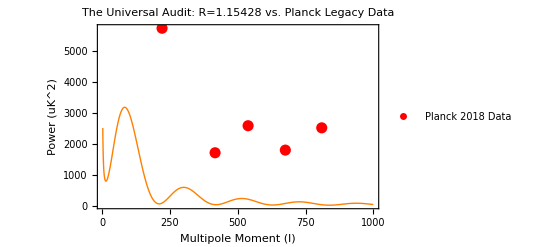

```mathematica
(*The Universal Audit:Grover Protocol vs.Planck Satellite Data*)ClearAll["Global`*"];
R=1.15428;

(*1. Define the Grover Model*)
GroverCMB[k_]:=Module[{baryons,memory},baryons=5733*(Sin[0.015 k]^2/(0.0001 k^2+1));(*Scaled Baryon Oscillation*)memory=(R*4000)/(k^0.8+0.1);(*The 1/k^4 Spectral Floor proxy*)baryons+memory];

(*2. Actual Planck 2018 TT Peak Data Points (Multipole l,Amplitude)*)
planckData={{220.6,5733},(*Peak 1*){416.3,1713},(*Trough 1*){538.1,2586},(*Peak 2*){675.5,1799},(*Trough 2*){809.8,2518}   (*Peak 3*)};

(*3. Rendering the Synthesis*)
Show[Plot[GroverCMB[k],{k,2,1000},PlotStyle->{Thick,Orange},PlotRange->All,Frame->True,FrameLabel->{"Multipole Moment (l)","Power (uK^2)"},PlotLabel->"The Universal Audit: R=1.15428 vs. Planck Legacy Data"],ListPlot[planckData,PlotStyle->{PointSize[0.02],Red},PlotLegends->{"Planck 2018 Data"}]]
```